```mathematica
(*Authored by Richard Chen
Created: 09/11/2024 3:32PM
Last Updated: 09/11/2024 3:32PM*)
```

## Exponential Function Approach

See how Chi_{n,n}(q) behaves as n grows for q integer

```mathematica
(*Note: the limit for when this expresssion stops running in a reasonable amount of time is degree 34*)
```

```mathematica
Solve[Coefficient[Series[(E^x+E^y-1)^q, {x,0,34},{y,0,34}],x*y,14]==0,q]
```

{{q→0},{q→1},{q→Root2.00Root[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,1]2.},{q→Root3.00Root[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,2]2.9999999999999996},{q→Root4.00Root[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,3]4.000000000063481},{q→Root5.00Root[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,4]4.99999957158495},{q→Root6.00Root[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,5]6.000924575312834},{q→Root6.80Root[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,6]6.797133602498913},{q→Root7.10-0.723 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,7]7.098715542057005},{q→Root7.10+0.723 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,8]7.098715542057005},{q→Root7.46-1.65 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,9]7.456595246227764},{q→Root7.46+1.65 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,10]7.456595246227764},{q→Root7.78-2.69 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,11]7.7824979579994364},{q→Root7.78+2.69 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,12]7.7824979579994364},{q→Root8.08-3.85 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,13]8.08049659231722},{q→Root8.08+3.85 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,14]8.08049659231722},{q→Root8.35-5.14 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,15]8.35441277304023},{q→Root8.35+5.14 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,16]8.35441277304023},{q→Root8.61-6.62 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,17]8.607964226045073},{q→Root8.61+6.62 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,18]8.607964226045073},{q→Root8.84-8.31 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,19]8.844916182319468},{q→Root8.84+8.31 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,20]8.844916182319468},{q→Root9.07-10.3 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,21]9.069728177701375},{q→Root9.07+10.3 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,22]9.069728177701375},{q→Root9.29-12.7 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,23]9.28894698585688},{q→Root9.29+12.7 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,24]9.28894698585688},{q→Root9.52-15.9 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,25]9.516697036979775},{q→Root9.52+15.9 ⅈRoot[2104263061425865873128963-6796285936247804243378067 #1+10312828834531949699241619 #1^2-9818093039186382362233653 #1^3+6604224586157434225899988 #1^4-3350021218471851926290938 #1^5+1335103286485251585742154 #1^6-429907099733458538686638 #1^7+114113228077789981596413 #1^8-25341251854980319708593 #1^9+«12»+32018605699795 #1^18-1539546407685 #1^19+62338646084 #1^20-2092470666 #1^21+56885816 #1^22-1208584 #1^23+18915 #1^24-195 #1^25+#1^26&,26]9.516697036979775}}

Look at Chi_ {n, n} (2)

```mathematica
chiTwo:=Table[Factorial[n]^2*Coefficient[Series[(E^x+E^y-1)^2, {x,0,n},{y,0,n}],x*y,n],{n,0,10}]
```

Look at Chi_ {n, n} (3)

```mathematica
chiThree:=Table[Factorial[n]^2*Coefficient[Series[(E^x+E^y-1)^3, {x,0,n},{y,0,n}],x*y,n],{n,0,10}]
```

Look at Chi_ {n, n} (4)

```mathematica
chiFour:=Table[Factorial[n]^2*Coefficient[Series[(E^x + E^y - 1)^4, {x, 0, n}, {y, 0, n}], x*y, n], {n, 0, 10}]
```

Look at Chi_ {n, n} (5)

```mathematica
chiFive:=Table[Factorial[n]^2*Coefficient[Series[(E^x+E^y-1)^5, {x,0,n},{y,0,n}],x*y,n],{n,0,10}]
```

```mathematica
chiList:={chiTwo,chiThree,chiFour,chiFive}
```

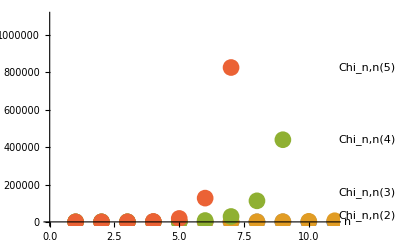

```mathematica
ListPlot[Table[Labeled[chiList[[j-1]],StringJoin[{"Chi_n,n(", ToString[j],")"}]],{j,2,5}],PlotStyle->PointSize[0.03],AxesLabel->{"n",""}]
```

```mathematica
Solve[Coefficient[Series[(E^x+E^y+E^z-1)^q, {x,0,10},{y,0,10},{z,0,10}],x*y,14]==0,q]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

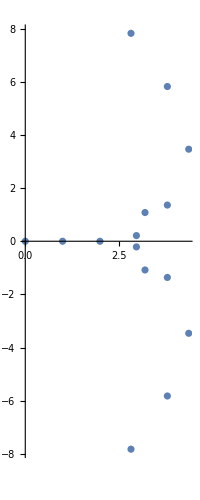

```mathematica
ComplexListPlot[q/.N[Solve[Coefficient[Series[(E^x+E^y+E^z-1)^q, {x,0,5},{y,0,5},{z,0,5}],x*y*z,5]==0,q]]]
```

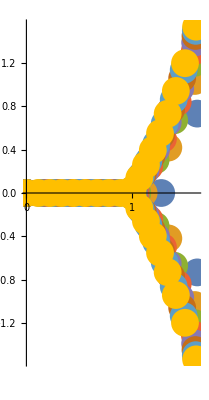

```mathematica
ComplexListPlot[Table[(q/n)/.Solve[Factorial[5]^3*Coefficient[Series[(E^x+E^y+E^z-2)^q, {x,0,n},{y,0,n},{z,0,n}],x*y*z,n]==0,q],{n,2,9}],PlotStyle->PointSize[0.05]]
```